# (Progress (Report))^2

## Reese Danzer and Karthik Boyareddygari

## I - User Manual

Step 1: Open “Main.nb”
Step 2: Scroll down to and evaluate the “interface[]” cell--as well as the initilization cells.
Step 3: Program is functional and interactive.

## II and III

Both parts two and three can be found in the set of files accompanying this one, since they are basically adaption of previous submissions and we are simply modifying those submissons.

## IV - Formulas

### Interpolation Across Datasets

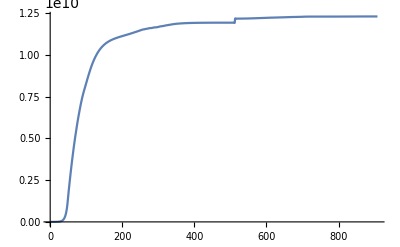
Our goal is to create a display that shows a star as a function of time. Our data sets possess a column with the age of the star, and sadly, the values for the age of the star are not lineraly distributed across every row of the dataset. As you can see from this graph of Row Number vs. Age (sorry its not labeled!) there are large gaps of time at the start of the dataset, and and a 2 million year jump in time towards the end:

-Graphics-
What this means is that we have to use age as our manipulate value, and we won’t be able to get away with using the row numbers in manipulate. This does pose somewhat of a problem, as row numbers are one of the key ways two dimensional data stores are organized, and are kind of a baseline necessity for most data functions. Add that to the fact that we’re attempting to create a continuous timeline and have to interpolate a lot, and we have a fairly major challenge.

To fix this we’ve written a function that will, once we finish it up, take the parameters of age, a quantity, and a function (generally intended to be the inverse of the function of row number vs age graphed above) and use the input age to determine the approprate row value and then interpolate the specified quantity from said row value. It is however, a work in progress, and we are considering alternative methods of solving this problem that may be more efficient.

## V - Files

### Star Data

Our project uses text files of data from an online site that provides complex star data for different masses of star (that site can be found here: http://www.astro.wisc.edu/~townsend/static.php?ref=ez-web#Using_EZ-Web).
The files are large tables of text readouts. Currently, we’re only working with and using the file for a single solar mass star, beacuse once we get that working we should be able to easily plug in the data for other mass stars. The files are stored next to our project file for ease of access.

## VI - Data Organization

### Datasets vs. Associations

We started the project with the intent to use datasets to store our data and have built our program to that intent. However, its becoming more and more apparent that it may be easier to just use associations and lists, because where the syntax of calling dataset values is dataset[row,”qty”], the syntax for a simple association with a list is qty[[row]], and that saves us some time and cpu power. So after this report, we’re going to switch to that.

## VII - Overview

Our code will create interactive diagrams of  astar using real data and databases as if the item shown were a real star. It will do this by interpolating data to create a continuous animation of the star’s life. 

Functions:
interface - The main function that brings the dataset interpolation together with the graphics to be put onscreen. Still in progress.
fancyInterpolation - A function that returns the value of a specified quantity, based on an intput age. Still in progress, and possibly due to be phased out.
connect - a function similar to Riffle, though it returns a 2D list of points. Finished.
alter - a function that creates a series of associations from an input data table. Finished

## VIII - Accomplishments

Since last report weve added to our interface, developed multiple methods for reading database information, and started connecting that data to our interface, primarily focusing on the sphere graphic and text readouts, since they are the simplest parts of our interface and thus apt for bug-testing the actual connections between the interface and the database. Getting the interface to work as a function of row number is fairly simple, but we need it working as a function of time, and thats proven to be more difficult.